# Notebook to solve the 2-patch 2 strain replicator like system.

(Run general.nb first)

```mathematica
eqA = thetaA*zA*(lam12(1-zA) -(lam12 + lam21)zA(1-zA)) - speed*(nuA - 1)(zB - zA);
eqB = thetaB*zB*(iot12(1-zB) - (iot12 + iot21)zB(1-zB)) - speed*(nuB -1)(zA-zB);
```

```mathematica
νA =FullSimplify[ (c (-2-μ (5+2 μ+R0 (-1+ω)+(2+μ) (1+2 μ) ω))+(1+μ) (2+μ (2+(3+2 μ) ω)))/(c (-1+R0) (2+μ (3+2 μ)) (1+μ ω))];
νB=FullSimplify[(-((1+μ) (2+μ ω) (1+2 μ ω))+c (2+μ (3+R0 (-1+ω)+ω (4+5 μ+2 μ (1+μ) ω))))/((-1+c R0) (1+μ) (2+μ ω (3+2 μ ω)))];
θA=2m/(2μ^2 + 3μ  + 2);
θB = 2m/(2(ω*μ)^2 + 3*ω*μ  + 2);
m = 1.5;
```

## Choose your parameters:

```mathematica
R0 = 2;
μ = 1;
c = 1;
ω = 1;
d = 1;
λ12 = 1;
λ21 = 1;
ι12 = 1;
ι21 = 1;
```

## Phase Plot:

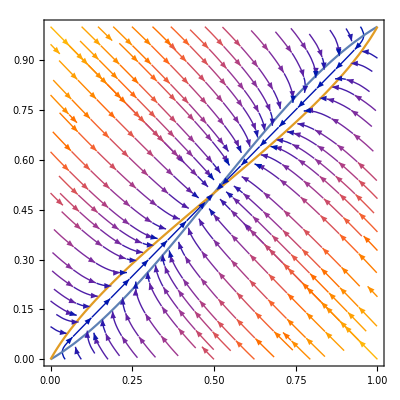

```mathematica
FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21]
```

## Stability Report:

```mathematica
eq = FreeEquilibria[c, ω, R0, μ, d, λ12, λ21, ι12, ι21];
StabilityReport[c, ω, R0, μ, d, λ12, λ21, ι12, ι21, eq]
```

({zA→1.,zB→1.} | False
{zA→0.5,zB→0.5} | True
{zA→0.,zB→0.} | False)

## Solution:

{{zA→InterpolatingFunction[…],zB→InterpolatingFunction[…]}}

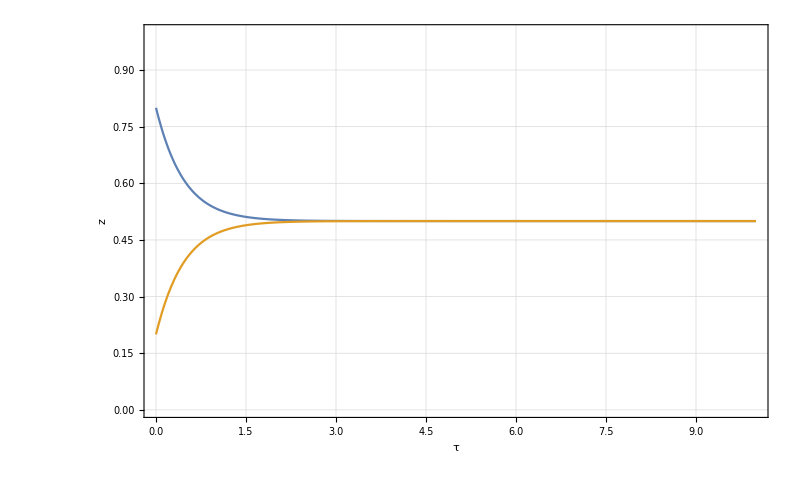

```mathematica
zA0 = 0.8;
zB0 =0.2;
sol = FreeSolution[c, ω, R0, μ, d, λ12, λ21, ι12, ι21, zA0, zB0]
Plot[{zA[t]/.sol, zB[t]/.sol},{t, 0, 10}, PlotRange->{0, 1}, PlotLegends->{"",""}, FrameLabel->{"τ", "z"}, PlotTheme->"Detailed", ImageSize-> 800]
```